```mathematica
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
{COLS,SEL}={{hexToRGB["#ee4266"],hexToRGB["#6ba5ff"]},False}
```

{{RGBColor[0.9333333333333333, 0.2588235294117647, 0.4],RGBColor[0.4196078431372549, 0.6470588235294118, 1.]},False}

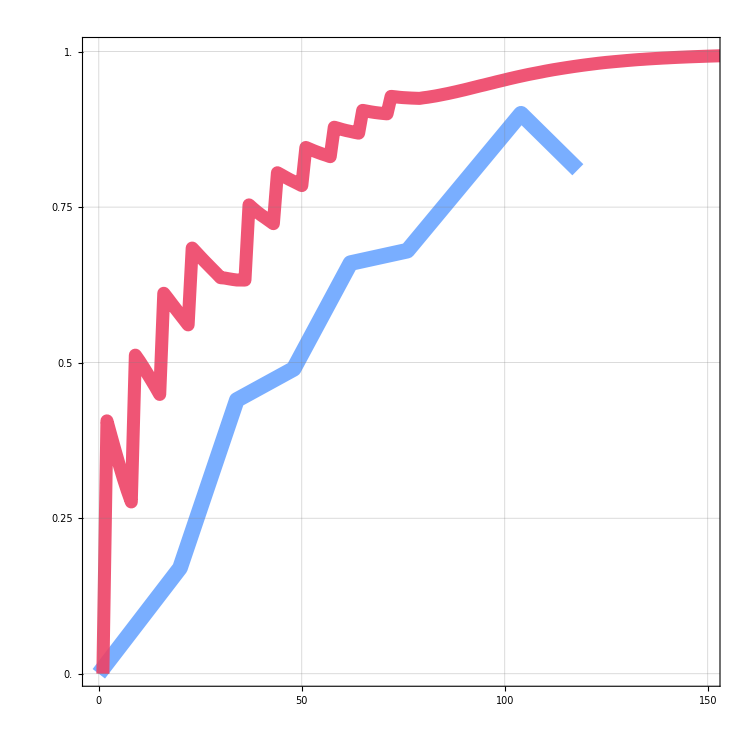

/Volumes/marshallShare/ThresholdResub/factorialSweep/Gordonvale/2019_10_11_ANALYZED/Gordonvale.pdf

```mathematica
RELSTART=20;
(*--------------------------------------------*)
If[
SEL,
ID="YorkeysKnob";
PATH ="/Volumes/marshallShare/ThresholdResub/factorialSweep/5percent/2019_10_08_ANALYZED/";
dataRaw={
{{04,01,2011},0.00},{{19,01,2011},0.24},{{01,02,2011},0.70},{{09,02,2011},0.62},{{16,02,2011},0.38},
{{02,03,2011},0.88},{{16,03,2011},0.76},{{30,03,2011},0.98},{{13,04,2011},1.00},{{27,04,2011},0.95}
};
,
ID="Gordonvale";
PATH="/Volumes/marshallShare/ThresholdResub/factorialSweep/Gordonvale/2019_10_11_ANALYZED/";
dataRaw={
{{04,01,2011},0.00},{{24,01,2011},0.17},{{07,02,2011},0.44},{{21,02,2011},0.49},{{07,03,2011},0.66},
{{21,03,2011},0.68},{{18,04,2011},0.90},{{02,05,2011},.81}
};
]
dataDates={DateObject[Reverse[#[[1]]]],#[[2]]}&/@dataRaw;
firstDate=dataDates[[1,1]];
dataExp={DateDifference[firstDate,#[[1]],"Day"][[1]],#[[2]]}&/@dataDates;
(*--------------------------------------------*)
files=FileNames["E_*10_0500*.csv",PATH];
rawData=Import[files[[1]]];
(*--------------------------------------------*)
ratios=1-rawData[[RELSTART;;All]][[All,4]];
ListLinePlot[{dataExp,ratios}
,AspectRatio->1
,Frame->True
,FrameStyle->Directive[{Opacity[1],hexToRGB["#141759"],Thickness[.015]}]
,FrameTicks->{{Range[0,1.2,.25],None},{Range[0,365,50],None}}
,FrameTicksStyle->Directive[{0.011}]
,GridLines->{Range[0,365,50],Range[0,1,.25]}
,ImageSize->750
,InterpolationOrder->1
,PlotRange->{{-1,150},{0,1.0025}}
,PlotStyle->{Directive[{Thickness[.015],Opacity[.9],COLS[[2]]}],Directive[{Thickness[.0125],Opacity[.9],COLS[[1]]}]}
]
Export[PATH<>ID<>".pdf",%,ImageSize->750]
```